Рассмотрим интегралы I1 и I2:

```mathematica
I1=Integrate[(1-((1-Sqrt[1-ϵ^2/x^2])/(1+Sqrt[1-ϵ^2/x^2]))^2)*x,{x,ϵ,1}]
```

ConditionalExpression[(2 (-2+3 ϵ^2-ϵ^6+2 √(1-ϵ^2)-2 ϵ^2 √(1-ϵ^2)))/(3 ϵ^4),((Re[ϵ/(1-ϵ)]≥0&&ϵ≠0)||ϵ/(1-ϵ)∉Reals||Re[ϵ/(1-ϵ)]<-1)&&(Re[ϵ]>1||(ϵ∉Reals&&(Re[ϵ]≥0||Re[(ϵ^2 (Im[ϵ]^2+(-1+Re[ϵ]) Re[ϵ])^2)/((Im[ϵ]^2+Re[ϵ] (-ϵ+Re[ϵ]))^2)]≤1))||0<Re[ϵ]<1)]

```mathematica
I1=Expand[Simplify[I1,Assumptions->{0<ϵ<1}]]
```

-4/(3 ϵ^4)+2/ϵ^2-(2 ϵ^2)/3+(4 √(1-ϵ^2))/(3 ϵ^4)-(4 √(1-ϵ^2))/(3 ϵ^2)

В матлабовском коде встречается следующее выражение для того же интеграла:

```mathematica
I1m = 1/2 *(ϵ^2 + 1/ϵ^2) - 1 + (1/4)*(1-2/ϵ^2)*Sqrt[1-ϵ^2]-(ϵ^2/8)*Log[ϵ^2/(2-ϵ^2+2*Sqrt[1-ϵ^2])]
```

-1+1/4 (1-2/ϵ^2) √(1-ϵ^2)+1/2 (1/ϵ^2+ϵ^2)-1/8 ϵ^2 Log[ϵ^2/(2-ϵ^2+2 √(1-ϵ^2))]

На графике видно, что кто-то очень неправ

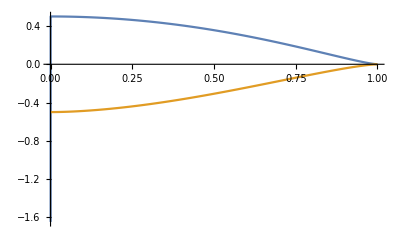

```mathematica
Plot[{I1, I1m},{ϵ,0,1}]
```

Теперь второй интеграл

```mathematica
I2=Integrate[(1-((1-Sqrt[1-ϵ^2/x^2])/(1+Sqrt[1-ϵ^2/x^2]))^2)*x^2,{x,ϵ,1}]
```

ConditionalExpression[(4 (-30+42 ϵ^2-12 ϵ^7+30 √(1-ϵ^2)-27 ϵ^2 √(1-ϵ^2)-ϵ^4 √(1-ϵ^2)-2 ϵ^6 √(1-ϵ^2)))/(105 ϵ^4),((Re[ϵ/(1-ϵ)]≥0&&ϵ≠0)||ϵ/(1-ϵ)∉Reals||Re[ϵ/(1-ϵ)]<-1)&&(Re[ϵ]>1||(ϵ∉Reals&&(Re[ϵ]≥0||Re[(ϵ^2 (Im[ϵ]^2+(-1+Re[ϵ]) Re[ϵ])^2)/((Im[ϵ]^2+Re[ϵ] (-ϵ+Re[ϵ]))^2)]≤1))||0<Re[ϵ]<1)]

```mathematica
I2=Expand[Simplify[I2,Assumptions->{0<ϵ<1}]]
```

-8/(7 ϵ^4)+8/(5 ϵ^2)-(16 ϵ^3)/35-(4 √(1-ϵ^2))/105+(8 √(1-ϵ^2))/(7 ϵ^4)-(36 √(1-ϵ^2))/(35 ϵ^2)-8/105 ϵ^2 √(1-ϵ^2)

```mathematica
I2m = (2/3)*(1-ϵ^3)+(2/3)*(1-ϵ^2)^(3/2)-(2/(5*ϵ^2))*(1-ϵ^5)+(2/(5*ϵ^2))*(1-ϵ^2)^(5/2)
```

2/3 (1-ϵ^2)^(3/2)+(2 (1-ϵ^2)^(5/2))/(5 ϵ^2)+2/3 (1-ϵ^3)-(2 (1-ϵ^5))/(5 ϵ^2)

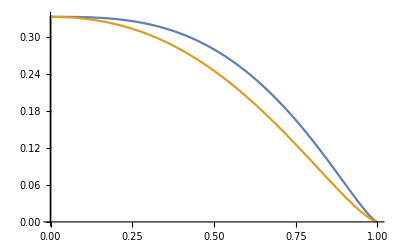

```mathematica
Plot[{I2,I2m},{ϵ,0,1}]
```

Здесь уже больше похоже на правду